# Introduction to Mathematica

## #CA1 #Q1 Signals & Systems Mohammad GharehHasanloo

```mathematica
X1[x_]:=Piecewise[{{0-Ramp[x+1]+ UnitStep[x]+2Ramp[x]-Ramp[x-1]-Ramp[x-2]+Ramp[x-3], -3≤x≤8}}]
X2[x_]:=Piecewise[{{0+ UnitStep[x+2] - 2UnitStep[x+1] + Ramp[x]+UnitStep[x-1] - Ramp[x-1] -UnitStep[x-2], -3≤x≤8}}]
```

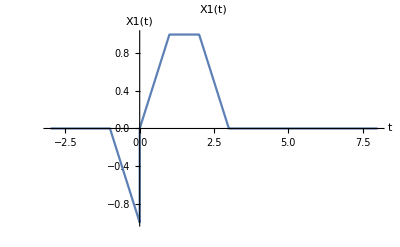

```mathematica
Plot[X1[x], {x, -3, 8},PlotLabel->"X1(t)",AxesLabel->{"t","X1(t)"}]
```

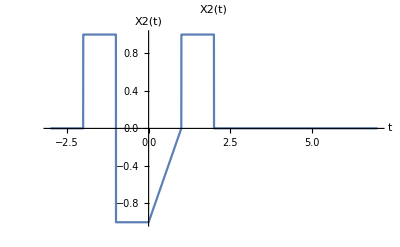

```mathematica
Plot[X2[x], {x, -3, 7},PlotLabel->"X2(t)",AxesLabel->{"t","X2(t)"}]
```

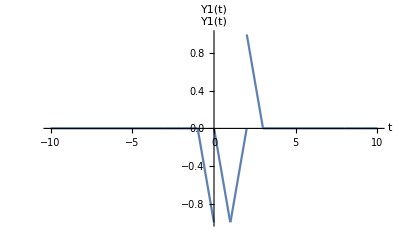

```mathematica
Y1[x_] := X1[x]*X2[x - 1]
Plot[Y1[x], {x, -10, 10},PlotLabel->"Y1(t)",AxesLabel->{"t","Y1(t)"}]
```

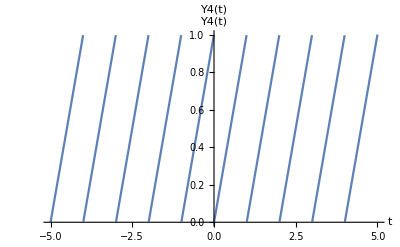

```mathematica
Y4[x_]:=∑_(k=-5)^5 X1[x-2*k]*X2[-1-x+2*k]
Plot[Y4[x], {x, -5, 5},PlotLabel->"Y4(t)",AxesLabel->{"t","Y4(t)"}]
```

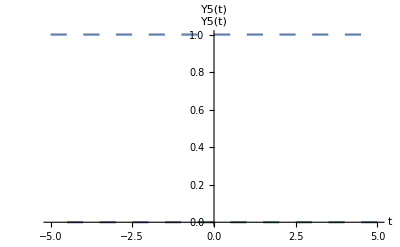

```mathematica
Y5[x_] := UnitStep[Y4[x]+1/2]-UnitStep[Y4[x]-1/2]
Plot[Y5[x], {x, -5, 5},PlotLabel->"Y5(t)",AxesLabel->{"t","Y5(t)"}]
```

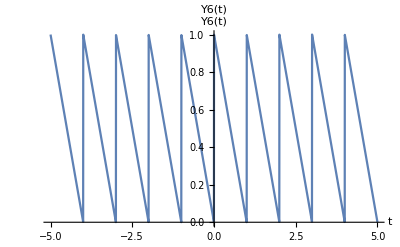

```mathematica
Y6[x_] := Ramp[Y4[x]+1]-2Ramp[Y4[x]]+Ramp[Y4[x]-1]
Plot[Y6[x], {x, -5, 5},PlotLabel->"Y6(t)",AxesLabel->{"t","Y6(t)"}]
```